```mathematica
(*-----------------------------------------------Calculating Pressure in Luna Series-----------------------------------------------*)
ClearAll["Global`*"]
g=9.81(*m/sec^2*); μw = 8.9*10^4(*Pa s*);ha=35.7*10^-3(*mm*); hc=6.4*10^-3(*mm*);Qmax=100 (*uL/min*); 
L1c=3.0(*mm*);w1c=3.0(*mm*);L1a=L1c+2*2.335(*mm*);w1a=.078(*mm*);
L2c=4.0(*mm*);w2c=2.0(*mm*);L2a=L2c+2*1.812(*mm*);w2a=.080(*mm*);
L3c=6.0(*mm*);w3c=2.0(*mm*);L3a=L3c+2*1.812(*mm*);w3a=.080(*mm*);
B[P_,ρ_,V_,h_]:= P+1/2 ρ*V^2+ρ*g*h;
R[L_,w_,h_]:=(12*L)/(w*h^3)*(1-(192*h)/(π^5*w))^-1;
Rtot[Lc_,wc_,La_,wa_]:= (2*(R[La,wa,ha])^-1+(R[Lc,wc,hc])^-1)^-1*μw; (*Units of mm^-3 x Pascal Seconds *)
L1R = Rtot[L1c,w1c,L1a,w1a];
L2R = Rtot[L2c,w2c,L2a,w2a];
L3R = Rtot[L3c,w3c,L3a,w3a] ;(*Has the largest resistance of the 3, use this to set upper bound*)

ΔP1 = Qmax*L1R *(.01667); (*Maximum L1 pressure drop in [Pa], .01667 converts (uL/min)*(Pa*s)*(mm^-3) to Pa*)
ΔP2 = Qmax*L2R *(.01667); (*Maximum L2 pressure drop in [Pa], .01667 converts (uL/min)*(Pa*s)*(mm^-3) to Pa*)
ΔP3 = Qmax*L3R *(.01667); (*Maximum L3 pressure drop in [Pa], .01667 converts (uL/min)*(Pa*s)*(mm^-3) to Pa*)
```

Converting the desired chamber flowrates to the flowrates I should source at the pump:

(Q_l = Cell Loading Flowrate at Pump;   Q_g = Cell Growth Flowrate at Pump)

Luna 1:  Q_l = 4582.17 [nL/min];  Q_g = 219.944 [nL/min]

Luna 2:  Q_l = 7961.75 [nL/min];  Q_g = 382.164 [nL/min]

Luna 3:  Q_l = 9188.26 [nL/min];  Q_g = 441.036 [nL/min]

Duty Cycles for approximating target Q_g, as it is below 5[μL/min]:

(t_p= Dispense time;  t_w= Wait time)

Luna 1:  t_p = 1000 [ms];  t_w = 21733 [ms]

Luna 2:  t_p = 1000 [ms];  t_w = 12083 [ms]

Luna 3:  t_p = 1000 [ms];  t_w = 10337 [ms]

(<Q_g>= Average flowrate from duty-cycle;   Q_g-<Q_g>= Difference between target flowrate and approximate.)

Luna 1:  <Q_g> = 219.945 [nL/min];  Q_g-<Q_g> = -0.00030389 [nL/min]

Luna 2:  <Q_g> = 382.175 [nL/min];  Q_g-<Q_g> = -0.0115404 [nL/min]

Luna 3:  <Q_g> = 441.034 [nL/min];  Q_g-<Q_g> = 0.00259137 [nL/min]

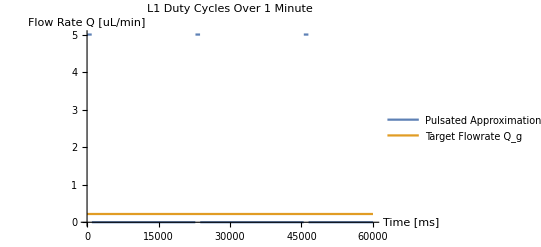

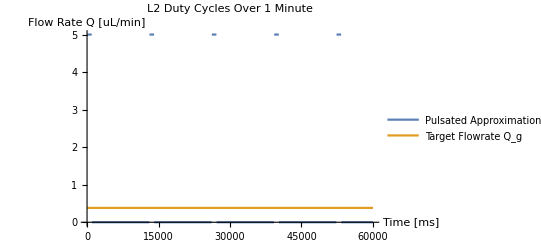

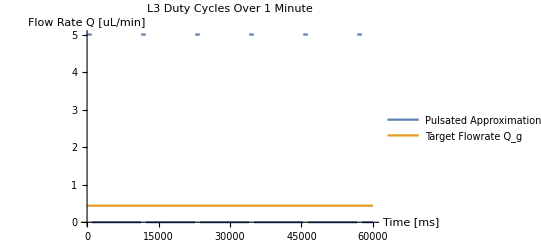

```mathematica
(*--------------------------------- Finding LSPone Flowrates given Luna Flow division. 1/24/2022 ----------------------------------*)

ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];(*Dir is notebook dir*)
(*Assuming Chamber Height 6.4μm, alt channels 35.7μm from luna series*)
{{r1},{r2},{r3}}=Import["Luna_Series_r1r2r3.dat"];(*Dir is notebook dir. Each r is Subscript[Q, chamber]/Subscript[Q, input] for respective Luna type*)
Vmin =500000/24000; (*LSPone minimum pickup/dispense volume in [nL], 500μL/24000*)
tstep = 250; (*Time in [ms] needed by LSPone to pickup/dispense 1 step, i.e. the minimum volume.*)
Nstep= 4; (*Number of steps to take per pulse. Higher Nstep hould help with flowrate fidelity at the microstepper, but decrease flow homogeneity.*)
Qcl=1250.0;(*Target Chamber loading flowrate, in [nL/min]*)
Qcg=60.0;(*Target Chamber growth flowrate, in [nL/min]*)

Ql1=Qcl/r1; Ql2=Qcl/r2; Ql3=Qcl/r3;
Qg1=Qcg/r1; Qg2=Qcg/r2; Qg3=Qcg/r3;
Print[Style["Converting the desired chamber flowrates to the flowrates I should source at the pump:",FontColor-> Red]];
Print[Style["(Q_l = Cell Loading Flowrate at Pump;   Q_g = Cell Growth Flowrate at Pump)",FontColor-> Blue]];
Print[Style["Luna 1:  ",FontColor->Orange],"Q_l = ",Ql1," [nL/min]", ";  Q_g = ",Qg1," [nL/min]"]; (* Target Input Flowrates for Luna 1 *)
Print[Style["Luna 2:  ",FontColor->Orange],"Q_l = ",Ql2," [nL/min]", ";  Q_g = ", Qg2," [nL/min]"]; (* Target Input Flowrates for Luna 2 *)
Print[Style["Luna 3:  ",FontColor->Orange],"Q_l = ",Ql3," [nL/min]", ";  Q_g = ",Qg3," [nL/min]"]; (* Target Input Flowrates for Luna 3 *)
Print[""];


(*Find the duty cycle that approximates the desired continuous input flow rate, with single steps delivered in 250ms at high res*)
Print[Style["Duty Cycles for approximating target Q_g, as it is below 5[μL/min]:",FontColor->Red]];
Print[Style["(t_p= Dispense time;  t_w= Wait time)",FontColor->Blue]]
tw1 = Round[((Nstep*Vmin)/Qg1)*(6*10^4)-Nstep*tstep];(*Factor (6*10^4) converts [min] to [ms]*)
tw2 = Round[((Nstep*Vmin)/Qg2)*(6*10^4)-Nstep*tstep];(*Factor (6*10^4) converts [min] to [ms]*)
tw3 =Round[((Nstep*Vmin)/Qg3)*(6*10^4)-Nstep*tstep];(*Factor (6*10^4) converts [min] to [ms]*)
Print[Style["Luna 1:  ",FontColor->Orange],"t_p = ",Nstep*tstep," [ms];","  t_w = ",tw1," [ms]"]; 
Print[Style["Luna 2:  ",FontColor->Orange],"t_p = ",Nstep*tstep," [ms];","  t_w = ",tw2," [ms]"]; 
Print[Style["Luna 3:  ",FontColor->Orange],"t_p = ",Nstep*tstep," [ms];","  t_w = ",tw3," [ms]"]; 


Print[Style["(<Q_g>= Average flowrate from duty-cycle;   Q_g-<Q_g>= Difference between target flowrate and approximate.)",FontColor->Blue]]
Print[Style["Luna 1:  ",FontColor->Orange],"<Q_g> = ", N[(Nstep*Vmin)/((Nstep*tstep+tw1)/(6*10^4))]," [nL/min];", "  Q_g-<Q_g> = ",Qg1-(Nstep*Vmin)/((Nstep*tstep+tw1)/(6*10^4))," [nL/min]"];
Print[Style["Luna 2:  ",FontColor->Orange],"<Q_g> = ", N[(Nstep*Vmin)/((Nstep*tstep+tw2)/(6*10^4))]," [nL/min];", "  Q_g-<Q_g> = ",Qg2-(Nstep*Vmin)/((Nstep*tstep+tw2)/(6*10^4))," [nL/min]"];
Print[Style["Luna 3:  ",FontColor->Orange],"<Q_g> = ", N[(Nstep*Vmin)/((Nstep*tstep+tw3)/(6*10^4))]," [nL/min];", "  Q_g-<Q_g> = ",Qg3-(Nstep*Vmin)/((Nstep*tstep+tw3)/(6*10^4))," [nL/min]"];
rectWave[t_,period_,duty_]:=5*UnitBox[Mod[t/period,1.]/(2.duty)]; (*Rectangle wave with amplitude in [uL]*)
Print[""];
Plot[{rectWave[t,Nstep*tstep+tw1,(Nstep*tstep)/(Nstep*tstep+tw1)],Qg1/1000},{t,0,6*10^4},PlotRange->Full,PlotLabel->Style["L1 Duty Cycles Over 1 Minute",FontColor-> Red],AxesLabel->{"Time [ms]","Flow Rate Q [uL/min]"},PlotLegends-> {"Pulsated Approximation <Q_g>","Target Flowrate Q_g"}]
Plot[{rectWave[t,Nstep*tstep+tw2,(Nstep*tstep)/(Nstep*tstep+tw2)],Qg2/1000},{t,0,6*10^4},PlotRange->Full,PlotLabel->Style["L2 Duty Cycles Over 1 Minute",FontColor-> Red],AxesLabel->{"Time [ms]","Flow Rate Q [uL/min]"},PlotLegends->{"Pulsated Approximation <Q_g>","Target Flowrate Q_g"}]
Plot[{rectWave[t,Nstep*tstep+tw3,(Nstep*tstep)/(Nstep*tstep+tw3)],Qg3/1000},{t,0,6*10^4},PlotRange->Full,PlotLabel->Style["L3 Duty Cycles Over 1 Minute",FontColor-> Red],AxesLabel->{"Time [ms]","Flow Rate Q [uL/min]"},PlotLegends->{"Pulsated Approximation <Q_g>","Target Flowrate Q_g"}]
```